# Math 223: Homework 7

Maia Powell

18 March 2021

## Problem 1

#### Find the first two terms of the asymptotic expansion of (∫_5)^9 e^-xt/t dt, x→ +∞

We will begin by performing Integration by Parts: 

(∫_5)^9 e^-xt/t dt = (∫_5)^9 1/t e^-xt dt 

u=1/t, dv= e^-xt
du = -1/t^2dt, v = -ⅇ^(-t x)/x

-ⅇ^(-t x)/x1/t(|_5)^9 - (∫_5)^9(-ⅇ^(-t x)/x)(-1/t^2dt)
= -ⅇ^(-t x)/tx(|_5)^9 - (∫_5)^9ⅇ^(-t x)/xt^2dt
= -ⅇ^(-9 x)/(9x)+ⅇ^(-5 x)/(5x)- (∫_5)^9ⅇ^(-t x)/xt^2dt

We thus find that the first term in the asymptotic expansion is -ⅇ^(-9 x)/(9x)+ⅇ^(-5 x)/(5x). Performing Integration by Parts once more: 

u = 1/t^2, dv = ⅇ^(-t x)/x
du = -2/t^3, v = -ⅇ^(-t x)/x^2

-ⅇ^(-t x)/x^21/t^2 (|_5)^9- (∫_5)^9(-ⅇ^(-t x)/x^2)(-2/t^3)
= -ⅇ^(-t x)/(t^2 x^2)(|_5)^9- (∫_5)^9(2 ⅇ^(-t x))/(t^3 x^2)dt
= -ⅇ^(-9x)/(81 x^2)+ ⅇ^(-5 x)/(25 x^2)- (∫_5)^9(2 ⅇ^(-t x))/(t^3 x^2)dt

We find that the second term in the asymptotic expansion is -ⅇ^(-9x)/(81 x^2)+ ⅇ^(-5 x)/(25 x^2).

Thus, I(x)~ -ⅇ^(-9 x)/(9x)+ⅇ^(-5 x)/(5x) -ⅇ^(-9x)/(81 x^2)+ ⅇ^(-5 x)/(25 x^2) as x→^+∞.

```mathematica
Integrate[Exp[-x*t]/t,{t,5,9}]
```

ExpIntegralEi[-9 x]-ExpIntegralEi[-5 x]

```mathematica
Limit[ExpIntegralEi[-9 x]-ExpIntegralEi[-5 x],x-> Infinity]
```

0

```mathematica
Limit[(Exp[-9x]*Log[9] -Exp[-5x]*Log[5] + (-9+9*Log[9])*(x*Exp[-9x]) -  (-5+5*Log[5])*(x*Exp[-5x])), x-> Infinity]
```

0

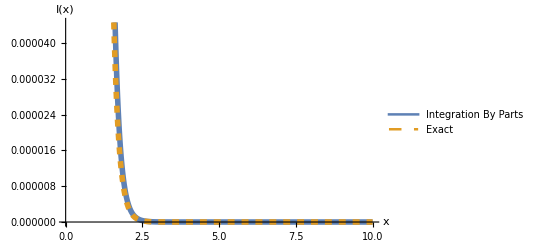

```mathematica
Plot[{-ⅇ^(-9 x)/(9x)+ⅇ^(-5 x)/(5x) -ⅇ^(-9x)/(81 x^2)+ ⅇ^(-5 x)/(25 x^2),ExpIntegralEi[-9 x]-ExpIntegralEi[-5 x]},{x,0,10},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Integration By Parts", "Exact"}]
```

## Problem 2

#### Use Watson’s lemma to determine the asymptotic expansion of I(x) = (∫_0)^π e^-xt t^(-1/3)cos(t)dt, x→ +∞

We first begin with the expansion of f(t) = (cos(t))/t^(1/3) about t = 0.

```mathematica
Collect[Series[Cos[t]/t^(1/3),{t,0,2}],t]
```

1/t^(1/3)-t^(5/3)/2

We then use this to implement Watson’s lemma:

```mathematica
Collect[Integrate[ ⅇ^(-x *t)Collect[Series[Cos[t]/t^(1/3),{t,0,2}],t], {t, 0, ∞}, Assumptions->x>0],x]
```

-(5 Gamma[2/3])/(9 x^(8/3))+Gamma[2/3]/x^(2/3)

Thus, we find that I(x)~-(5 Gamma[2/3])/(9 x^(8/3))+Gamma[2/3]/x^(2/3).

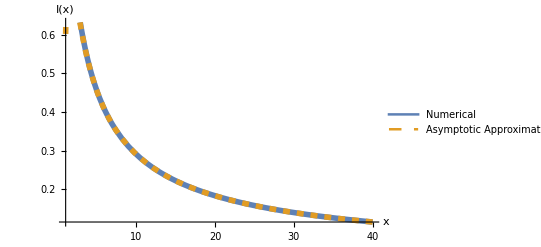

```mathematica
Plot[{NIntegrate[Cos[t]/t^(1/3)ⅇ^(-x *t),{t,0,π}],Collect[Integrate[ ⅇ^(-x *t)Collect[Series[Cos[t]/t^(1/3),{t,0,2}],t], {t, 0, ∞}, Assumptions->x>0],x]},{x,1,40},
PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Numerical","Asymptotic Approximation"}]
```

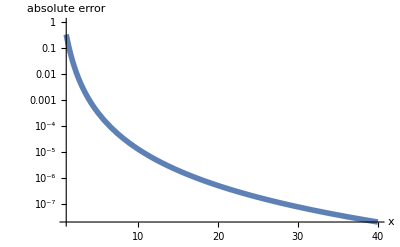

```mathematica
LogPlot[Abs[NIntegrate[Cos[t]/t^(1/3)ⅇ^(-x *t),{t,0,π}]-Collect[Integrate[ ⅇ^(-x *t)Collect[Series[Cos[t]/t^(1/3),{t,0,2}],t], {t, 0, ∞}, Assumptions->x>0],x]],{x,1,40},
PlotStyle-> Directive[Solid,Thickness[0.01]],AxesLabel->{Style["x",Italic,18],Style["absolute error", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

## Problem 3

#### Use Laplace’s method to determine the leading behavior of I(x) =(∫^(1/2))_(-1/2)e^(-xsin^4(t))dt, x→ +∞

For this problem, f(t) = 1 and ϕ(t) = sin^4(t). We first seek to find local minima on [-1/2,1/2].

```mathematica
Solve[D[Sin[t]^4,t]==0]
```

{{t→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{t→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ]},{t→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ]},{t→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

We choose t = 0 (this is when C[1]=0), because this is the only possible value presented that lies between -1/2 and 1/2.
We then expand about t = 0 and find the following:

```mathematica
Series[Sin[t]^4,{t,0,4}]
```

t^4+O[t]^5

Assuming sin(t) ~ t,  I(x) ∼ ∫_(-∞)^∞ ⅇ^(-x t^4)ⅆt ,   x→+∞. We can now integrate!

```mathematica
Integrate[ⅇ^(-x* t^4),{t,-∞,∞}, Assumptions->x>0]
```

(2 Gamma[5/4])/x^(1/4)

Thus, we find that I(x)~(2 Gamma[5/4])/x^(1/4).

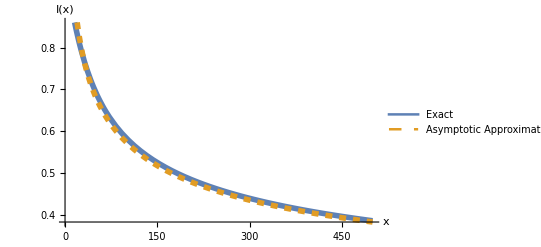

```mathematica
Plot[{NIntegrate[ⅇ^(-x Sin[t]^4),{t,-0.5,0.5}],(2 Gamma[5/4])/x^(1/4)},{x,1,500},
PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact","Asymptotic Approximation"}]
```